Autor: Krzysztof Dragon

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 4

Metoda predyktor-korektor

Napisać procedurę realizującą algorytm metody predyktor-korektor (argumenty:  f, x_0, y_0, b, n).
Jako metodę startową wykorzystać metodę Rungego-Kutty rzędu trzeciego. Jako metodę predykcji wykorzystać trzy krokową metodę Adamsa-Bashfortha, a jako metodę korekcji trzy krokową metodę Adamsa-Moultona. W metodzie korekcji wykonać dwie iteracje metody iteracji prostej.

Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

{y'(x)=2 sin x - y(x),  x∈[0,15],
y(0)=2.

Obliczenia wykonać dla 20 i 100 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.
Wyznaczyć także błędy maksymalne oraz średnie dla obu siatek.

## Rozwiązanie

```mathematica
(* Metoda Rungiego - Kutty rzędu 3-go *)
Clear[metodaRK3];
metodaRK3[f_,x0_,y0_,h_,n_] :=Module[{xw,yw,k1,k2,k3,wynik},
xw = Table[x0+i*h,{i,0,n}];
yw = Table[0,{i,0,n}];
yw[[1]] = y0;
Do[
k1=f[xw[[i]],yw[[i]]];
k2 = f[xw[[i]]+h/2,yw[[i]]+h*k1/2];
k3 = f[xw[[i+1]],yw[[i]]-h*k1+2*h*k2];
yw[[i+1]] = yw[[i]] + h/6*(k1+4k2+k3),
{i,1,n}];
wynik = Transpose[{xw,yw}];
Return[wynik]
]
```

```mathematica
(* Metoda Predyktor - Korektor *)
metodaPK[f_,x0_,y0_,b_,n_] := Module[{h,nmip,xw,yw,b31p,b32p,b33p,b30k,b31k,b32k,b33k,wp,m0,m1,m2,m3,η,wynik},

h = (b-x0)/n;
nmip = 2;
xw = Table[x0+i*h,{i,0,n}];
yw = Table[0,{i,0,n}];
yw[[1]] = y0;

b31p = 23/12;
b32p = -16/12;
b33p = 5/12;

b30k = 9/24;
b31k = 19/24;
b32k = -5/24;
b33k = 1/24;

wp = metodaRK3[f,x0,y0,h,2];

Do[yw[[i]] = wp[[i,2]], {i,2,3}];

m1 = f[xw[[3]], yw[[3]]];
m2 = f[xw[[2]], yw[[2]]];
m3 = f[xw[[1]], yw[[1]]];
Do[
(* Predykcja *)
η = yw[[i]] + h * (b31p*m1+b32p*m2+b33p*m3);

(* Korekcja *)
Do[
m0 = f[xw[[i+1]],η];
η = yw[[i]] + h * (b30k*m0 + b31k * m1+ b32k*m2+b33k*m3),{j,1,nmip}];

yw[[i+1]] = η;
m3 = m2;
m2 = m1;
m1 = f[xw[[i+1]],yw[[i+1]]],
{i,3,n}];

wynik  = Transpose[{xw,yw}];

Return[wynik];
];
```

```mathematica
f[x_,y_] := 2Sin[x] - y;
y0 = 2.;
x0 =0.;
b = 15;
n20 = 20;
n100 = 100;
```

```mathematica
wynik20 = metodaPK[f,x0,y0,b,n20]
```

{{0.,2.},{0.75,1.32121},{1.5,1.56074},{2.25,1.6921},{3.,1.25249},{3.75,0.290342},{4.5,-0.759005},{5.25,-1.37067},{6.,-1.23291},{6.75,-0.427383},{7.5,0.610293},{8.25,1.32172},{9.,1.32445},{9.75,0.616702},{10.5,-0.421865},{11.25,-1.234},{12.,-1.38392},{12.75,-0.791186},{13.5,0.226119},{14.25,1.12209},{15.,1.41592}}

```mathematica
wynik100 = metodaPK[f,x0,y0,b,n100]
```

{{0.,2.},{0.15,1.74271},{0.3,1.5625},{0.45,1.44728},{0.6,1.38563},{0.75,1.36695},{0.9,1.38134},{1.05,1.41959},{1.2,1.4732},{1.35,1.53438},{1.5,1.5961},{1.65,1.6521},{1.8,1.69691},{1.95,1.72593},{2.1,1.7354},{2.25,1.72242},{2.4,1.68499},{2.55,1.62196},{2.7,1.53305},{2.85,1.41878},{3.,1.28046},{3.15,1.1201},{3.3,0.940365},{3.45,0.744495},{3.6,0.53619},{3.75,0.319532},{3.9,0.0988721},{4.05,-0.121276},{4.2,-0.336348},{4.35,-0.541843},{4.5,-0.733426},{4.65,-0.90704},{4.8,-1.05899},{4.95,-1.18605},{5.1,-1.28552},{5.25,-1.35529},{5.4,-1.39392},{5.55,-1.40063},{5.7,-1.37537},{5.85,-1.31876},{6.,-1.23215},{6.15,-1.11754},{6.3,-0.977534},{6.45,-0.815331},{6.6,-0.634604},{6.75,-0.439442},{6.9,-0.234252},{7.05,-0.0236663},{7.2,0.187568},{7.35,0.394692},{7.5,0.593037},{7.65,0.77814},{7.8,0.945831},{7.95,1.09234},{8.1,1.21436},{8.25,1.30915},{8.4,1.37457},{8.55,1.40916},{8.7,1.41212},{8.85,1.3834},{9.,1.32362},{9.15,1.23414},{9.3,1.11695},{9.45,0.974696},{9.6,0.810559},{9.75,0.628229},{9.9,0.431797},{10.05,0.225675},{10.2,0.0144909},{10.35,-0.197014},{10.5,-0.40409},{10.65,-0.602087},{10.8,-0.786559},{10.95,-0.953364},{11.1,-1.09876},{11.25,-1.21947},{11.4,-1.3128},{11.55,-1.37664},{11.7,-1.40956},{11.85,-1.41083},{12.,-1.38041},{12.15,-1.31899},{12.3,-1.22795},{12.45,-1.10933},{12.6,-0.965798},{12.75,-0.800575},{12.9,-0.617371},{13.05,-0.420303},{13.2,-0.213795},{13.35,-0.00248501},{13.5,0.208881},{13.65,0.415555},{13.8,0.612898},{13.95,0.796476},{14.1,0.962167},{14.25,1.10625},{14.4,1.22549},{14.55,1.31721},{14.7,1.37934},{14.85,1.4105},{15.,1.40998}}

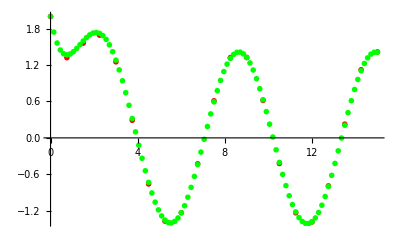

```mathematica
plt10 = ListPlot[wynik20, PlotStyle->{Red, PointSize[0.01]}, PlotRange -> All];
plt20 = ListPlot[wynik100, PlotStyle->{Green, PointSize[0.01]}, PlotRange -> All];
Show[plt10,plt20]
```

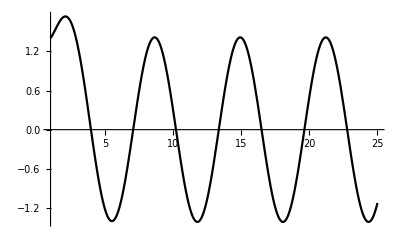

```mathematica
roz = DSolve[{y' [x]==   2Sin[x] - y[x],y[0] == 2}, y[x],x];
pdok = Plot[roz[[1,1,2]], {x,1,25}, PlotRange -> All, PlotStyle->{Black, PointSize[0.008]}]
```

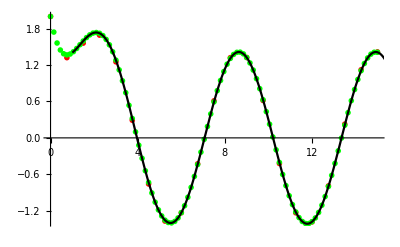

```mathematica
Show[plt10,plt20,pdok]
```

```mathematica
(* Wartości błędów dla n = 20 *)
ydok = Table[roz[[1,1,2]] /. {x->wynik20[[i,1]]},{i,1,Length[wynik20]}];
bledy20 = Table [{wynik20[[i,1]], Abs[wynik20[[i,2]] - ydok[[i]]]},{i,1,Length[wynik20]}]
```

{{0.,0.},{0.75,0.0458445},{1.5,0.0354065},{2.25,0.0303484},{3.,0.0279869},{3.75,0.0292094},{4.5,0.0255974},{5.25,0.0153903},{6.,0.000755858},{6.75,0.0120664},{7.5,0.0172687},{8.25,0.0125818},{9.,0.000828901},{9.75,0.0115335},{10.5,0.0177889},{11.25,0.0145403},{12.,0.0035098},{12.75,0.00939371},{13.5,0.0172512},{14.25,0.0158488},{15.,0.00594034}}

```mathematica
(* Wartości dokładne dla błędów n = 100 *)
ydok = Table[roz[[1,1,2]] /. {x->wynik100[[i,1]]},{i,1,Length[wynik100]}];
bledy100 = Table [{wynik100[[i,1]], Abs[wynik100[[i,2]] - ydok[[i]]]},{i,1,Length[wynik100]}]
```

{{0.,0.},{0.15,0.0000820813},{0.3,0.000140685},{0.45,0.00012289},{0.6,0.000108436},{0.75,0.0000947861},{0.9,0.0000825351},{1.05,0.0000716005},{1.2,0.0000619328},{1.35,0.0000534701},{1.5,0.0000461459},{1.65,0.0000398889},{1.8,0.0000346246},{1.95,0.0000302748},{2.1,0.0000267592},{2.25,0.0000239954},{2.4,0.0000218996},{2.55,0.0000203876},{2.7,0.000019375},{2.85,0.0000187785},{3.,0.0000185162},{3.15,0.0000185089},{3.3,0.0000186808},{3.45,0.0000189599},{3.6,0.0000192794},{3.75,0.0000195784},{3.9,0.0000198022},{4.05,0.0000199032},{4.2,0.0000198412},{4.35,0.0000195843},{4.5,0.0000191085},{4.65,0.0000183981},{4.8,0.000017446},{4.95,0.0000162529},{5.1,0.0000148275},{5.25,0.0000131858},{5.4,0.0000113505},{5.55,9.35043×10^-6},{5.7,7.21947×10^-6},{5.85,4.99584×10^-6},{6.,2.72095×10^-6},{6.15,4.38416×10^-7},{6.3,1.80709×10^-6},{6.45,3.97093×10^-6},{6.6,6.00958×10^-6},{6.75,7.88173×10^-6},{6.9,9.54926×10^-6},{7.05,0.0000109781},{7.2,0.0000121393},{7.35,0.0000130094},{7.5,0.000013571},{7.65,0.0000138138},{7.8,0.0000137339},{7.95,0.0000133348},{8.1,0.0000126267},{8.25,0.0000116268},{8.4,0.0000103586},{8.55,8.85139×10^-6},{8.7,7.13994×10^-6},{8.85,5.26332×10^-6},{9.,3.26432×10^-6},{9.15,1.18834×10^-6},{9.3,9.17521×10^-7},{9.45,3.00556×10^-6},{9.6,5.02853×10^-6},{9.75,6.94069×10^-6},{9.9,8.69882×10^-6},{10.05,0.0000102632},{10.2,0.0000115985},{10.35,0.0000126745},{10.5,0.000013467},{10.65,0.000013958},{10.8,0.0000141363},{10.95,0.0000139978},{11.1,0.0000135456},{11.25,0.0000127897},{11.4,0.000011747},{11.55,0.000010441},{11.7,8.90079×10^-6},{11.85,7.16101×10^-6},{12.,5.26068×10^-6},{12.15,3.24244×10^-6},{12.3,1.15158×10^-6},{12.45,9.64962×10^-7},{12.6,3.05968×10^-6},{12.75,5.08556×10^-6},{12.9,6.99711×10^-6},{13.05,8.75142×10^-6},{13.2,0.0000103091},{13.35,0.0000116352},{13.5,0.0000126999},{13.65,0.0000134794},{13.8,0.000013956},{13.95,0.0000141193},{14.1,0.0000139653},{14.25,0.0000134978},{14.4,0.000012727},{14.55,0.0000116705},{14.7,0.0000103518},{14.85,8.80058×10^-6},{15.,7.05173×10^-6}}

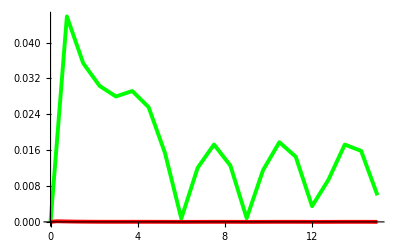

```mathematica
(* Wykres błędów *)
wb20 = ListPlot[bledy20, Joined->True, PlotStyle->{Green, Thickness -> 0.007}];
wb100 = ListPlot[bledy100, Joined->True, PlotStyle->{Red, Thickness -> 0.007}, PlotRange->All];
Show[wb20,wb100]
```

```mathematica
(* Błąd maksymalny dla n = 20 *)
Max[Transpose[bledy20][[2]]]
```

0.0458445

```mathematica
(* Błąd maksymalny dla n = 100 *)
Max[Transpose[bledy100][[2]]]
```

0.000140685

```mathematica
(* Średnia błędów dla n = 20 *)
Mean[Transpose[bledy20][[2]]]
```

0.0166234

```mathematica
(* Średnia błędów dla n = 100 *)
Mean[Transpose[bledy100][[2]]]
```

0.0000195709